```mathematica
f[x_]:=42*(x^5)*(1-x)
sol = Solve[y==x^3, x]
```

{{x→y^(1/3)},{x→-(-1)^(1/3) y^(1/3)},{x→(-1)^(2/3) y^(1/3)}}

```mathematica
D[x /. sol[[1]], {y}]
```

1/(3 y^(2/3))

```mathematica
f[x/.sol[[1]]]*D[x /. sol[[1]], y]
```

14 (1-y^(1/3)) y

```mathematica
Plot[E^(-x),{x,0,10}]
```

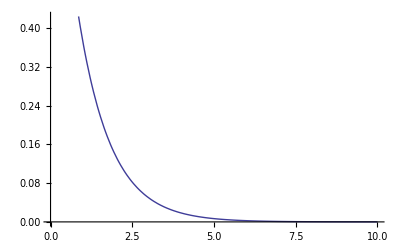

```mathematica
(*2.28*)
 a = Integrate[E^(-x),{x,0,Infinity}]
```

```mathematica
Subscript[μ, 3]=∫_0^∞ (x-1)^3/ⅇ^x ⅆx
```

2

```mathematica
(*2.33*)
Integrate[E^(t*x)/c,{x,0,c}]
```

(-1+ⅇ^(c t))/(c t)

```mathematica
a = Sum[λ^x/(x!*E^(λ - t*x)), {x, 0, Infinity}]
```

ⅇ^(-λ+ⅇ^t λ)

```mathematica
D[a, {t}] /. t->0
```

λ

```mathematica
D[(p*E^t - p + 1)^n, {t,2}] /. t -> 0
```

n p+(-1+n) n p^2

```mathematica
Integrate[x^(a-1)/(ⅇ^x a),{x,0,∞},Assumptions->a>0]/.x->b t
```

1